-Graphics-

## Lesson 5: linear first-order equations

-Graphics-

## Overview

The first class of differential equations to be discussed is first-order linear differential equations.

These differential equations take the form:

y'(x)+a_0(x)y(x)=g(x)

When a_o(x) and g(x) are both constant, the equation becomes much simpler and can be solved by straightforward integration.

For an arbitrary first-order linear ODE, there is a general method for solving the equation.

This method is due to Leibniz and it is known as the integrating factor method.

## Constant Coefficients

Begin with a general first-order linear differential equation with constant coefficients:

y'(x)+a y(x)=b

Assume that a≠0 and y(x)≠b/a and rewrite the equation as:

(y'(x))/(y(x)-b/a)=-a

With y'(x)=ⅆy/ⅆx, apply Integrate to both sides to obtain an expression involving y(x):

```mathematica
sln=Integrate[1/(y[x]-b/a),y[x]]==Integrate[-a,x,GeneratedParameters->C]
```

Log[-b+a y[x]]==-a x+C[1]

Solve the equation for y(x):

```mathematica
Solve[sln,y[x],Reals]
```

{{y[x]→(b+ⅇ^(-a x+C[1]))/a}}

Defining C=e^C_1/a as the arbitrary constant, the final expression for y(x) becomes:

y(x)=b/a+Ce^-ax

This function does indeed satisfy the differential equation:

```mathematica
(y'[x]+a*y[x]==b)/.y->Function[x,b/a+C*Exp[-a x]]//Simplify
```

True

This is a simple example of solving a differential equation through the use of a technique known as separation of variables, which will be discussed in more detail further on in the course.

## Example: Constant Coefficients

Solve the initial value problem and plot the corresponding solution on the direction field:

y'(x)=5 y(x)-2

y(0)=5

Using the previous result for equations with constant coefficients, this differential equation has the following solution:

y(x)=(-2+c e^(5x))/-5

Set y(0)=5 and use Solve to get the arbitrary constant:

```mathematica
Solve[(-2+C)/-5==5,C]
```

{{C→-23}}

Thus, after canceling a minus sign, the particular solution satisfying the initial conditions becomes:

y(x)=(2+23 e^(5 x))/5

Visualize the particular solution with the direction field:

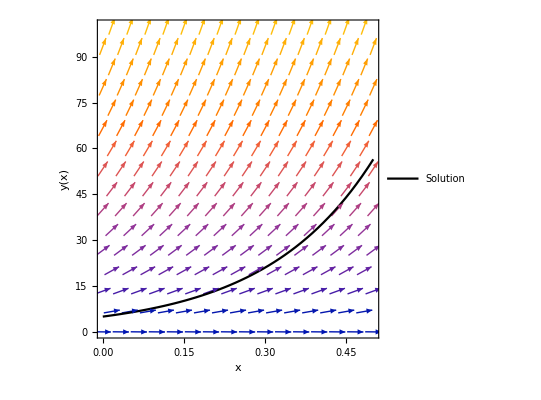

```mathematica
Show[VectorPlot[{1,5y-2},{x,0,1/2},{y,0,100},],Plot[(2+23Exp[5 x])/5,{x,0,1/2},],]
```

## Integrating Factor Method

The last method cannot be used in the general case where the coefficients are not constant.

In such a case, it is required to multiply the equation by an unknown function called the integrating factor.

The left-hand side of the equation then becomes the derivative of an expression involving the unknown function y(x).

This method can be used to obtain solutions to many first-order linear differential equations.

## Integrating Factor Method

Suppose it is necessary to solve the linear first-order differential equation:

y'(x)+p(x) y(x)=q(x)

Multiply the equation by an unknown function μ(x) known as the integrating factor:

μ(x)y'(x)+μ(x)p(x) y(x)=μ(x)q(x)

Compare the left-hand side of this equation with the product rule for differentiation:

ⅆ/ⅆx(μ(x)y(x))=μ(x)y'(x)+μ'(x)y(x)

These are identical if:

μ'(x)=μ(x)p(x)

Thus, to find the integrating factor, you must find a function μ(x) that satisfies this auxiliary equation.

## Integrating Factor Method

A good guess for the form of the integrating factor is e^x because the derivative of this function is the function itself.

The next step is searching for a more complex function that, when differentiated, produces the term p(x).

Using the chain rule from calculus:

ⅆ/ⅆx e^(f(x))=((ⅆf(x))/ⅆx)e^(f(x))

Use this to infer that the unknown function is:

μ(x)=e^(∫p(x)ⅆx)

This function satisfies the differential equation:

(ⅆμ(x))/ⅆx=μ(x)p(x)

Thus, the integrating factor is μ(x)=e^(∫p(x)ⅆx), and the differential equation becomes:

(ⅆy(x))/ⅆx e^(∫p(x)ⅆx)+p(x)y(x)e^(∫p(x)ⅆx)=q(x)e^(∫p(x)ⅆx)

## Integrating Factor Method

From the properties of the product rule, this simplifies to:

ⅆ/ⅆx(e^(∫p(x)ⅆx)y(x))=e^(∫p(x)ⅆx)q(x)

Integrating both sides with respect to x:

e^(∫p(x)ⅆx)y(x)=∫e^(∫p(x)ⅆx)q(x)ⅆx+C_1

Solving for y(x), the general solution takes the form:

y(x)=(∫e^(∫p(x)ⅆx)q(x)ⅆx+C_1)/e^(∫p(x)ⅆx)

The integrating factor method is a useful tool for solving first-order linear differential equations when the integrals exist.

## Example 1

Solve the linear first-order differential equation:

y'(x)+1/x y(x)=sin(x)

y(π)=0

First, define the functions p(x) and q(x):

```mathematica
p[x_]:=1/x
q[x_]:=Sin[x]
```

Define the integrating factor e^(∫p(x)ⅆx):

```mathematica
integratingFactor=Exp[Integrate[p[x],x]]
```

x

Use the integrating factor to find the solution y(x)=(∫e^(∫p(x)ⅆx)q(x)ⅆx+C_1)/e^(∫p(x)ⅆx):

```mathematica
sln=(1/integratingFactor)*(Integrate[integratingFactor*q[x],x,GeneratedParameters->C])
```

(C[1]-x Cos[x]+Sin[x])/x

Verify the result with DSolveValue:

```mathematica
DSolveValue[y'[x]+p[x] y[x]==q[x],y[x],x]
```

C[1]/x+(-x Cos[x]+Sin[x])/x

## Example 1

Now solve for C[1] so that the function satisfies the initial condition y(π)=0:

```mathematica
constant=Solve[(sln==0/.x->Pi),C[1]][[1]]
```

{C[1]→-π}

Plot the particular solution and visualize the direction field with VectorPlot:

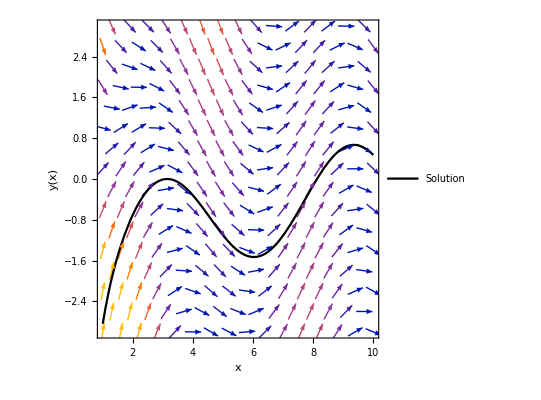

```mathematica
Show[VectorPlot[{1,-y/x+Sin[x]},{x,1,10},{y,-3,3},],Plot[(sln/.constant),{x,1,10},],]
```

## Example 2

Solve the linear first-order differential equation:

x y'(x)+(x+1)y(x)=e^x

y(1)=0

Begin by defining the functions necessary to solve the problem:

```mathematica
p[x_]:=(x+1)/x
q[x_]:=Exp[x]/x
```

Calculate the integrating factor:

```mathematica
integratingFactor=Exp[Integrate[p[x],x]];
```

Use the integrating factor to find the general solution:

```mathematica
sln=(1/integratingFactor)*(Integrate[integratingFactor*q[x],x,GeneratedParameters->C])//Expand
```

ⅇ^x/(2 x)+(ⅇ^-x C[1])/x

Verify with DSolveValue:

```mathematica
DSolveValue[ y'[x]+p[x]y[x]==q[x],y[x],x]
```

ⅇ^x/(2 x)+(ⅇ^-x C[1])/x

## Example 2

Solve for C[1] so that the function satisfies the initial condition y(1)=30:

```mathematica
constant=Solve[(sln==30)/.x->1,C[1]][[1]]
```

{C[1]→-1/2 (-60+ⅇ) ⅇ}

Create a plot to see how the solution compares to other solutions:

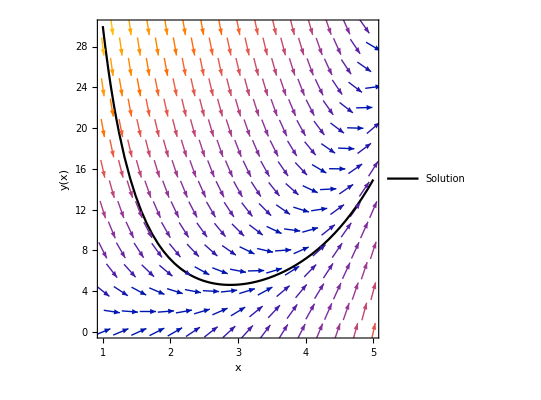

```mathematica
Show[VectorPlot[{1,-(1+x)*y/x+Exp[x]/x},{x,1,5},{y,0,30},],Plot[(sln/.constant),{x,1,5},],]
```

## Summary

This lesson discussed first-order linear differential equations.

These differential equations take the form:

y'(x)+a_o(x)y(x)=g(x)

When the coefficients are constant, it has been proved that the solutions take the form:

y(x)=b/a+C[1] e^(-a x)

The integrating factor method can be used to solve an arbitrary first-order linear ODE.

Solutions to these equations have a general form of:

y(x)=(∫e^(∫p(x)ⅆx)q(x)ⅆx+C[1])/e^(∫p(x)ⅆx)

The next lesson will discuss a different class of first-order equations called separable equations.